```mathematica
TrueV=Import["C:\\Users\\ASUS\\Documents\\Lepage_TrueV.dat","CSV"]
```

{{0.307487,-5.73494},{0.320856,-5.47289},{0.336898,-5.15663},{0.360963,-4.80422},{0.379679,-4.53313},{0.395722,-4.30723},{0.417112,-4.05422},{0.454545,-3.64759},{0.513369,-3.15964},{0.548128,-2.91566},{0.585561,-2.68072},{0.631016,-2.46386},{0.679144,-2.23795},{0.73262,-2.03916},{0.791444,-1.85843},{0.852941,-1.69578},{0.919786,-1.54217},{0.986631,-1.39759},{1.05615,-1.28916},{1.12834,-1.17169},{1.20588,-1.09036},{1.28075,-1.00904},{1.35561,-0.945783},{1.43316,-0.873494},{1.5107,-0.819277},{1.58824,-0.76506},{1.66578,-0.71988},{1.74332,-0.683735},{1.82353,-0.64759},{1.90374,-0.611446},{1.98128,-0.575301},{2.05882,-0.566265},{2.13904,-0.53012},{2.21925,-0.503012},{2.29679,-0.48494},{2.37433,-0.475904},{2.45455,-0.448795},{2.53476,-0.439759},{2.6123,-0.421687},{2.77005,-0.394578},{2.92781,-0.36747},{3.13369,-0.331325},{3.35561,-0.304217}}

```mathematica
Model=-1/r+a (E^(-b r^2))/r;
Model2=-1/r+a(E^(-b r^2))/r+c E^(-d r)/r;
FindFit[TrueV,Model,{a,b},r]
FindFit[TrueV,Model2,{a,b,c,d},r]
Modelf[r_]=Model/.%%
Modelf2[r_]=Model2/.%%
```

{a→-0.793895,b→0.739369}

{a→-0.120009,b→2.50727,c→-0.875409,d→0.865025}

-1/r-(0.793895 ⅇ^(-0.739369 r^2))/r

-1/r-(0.875409 ⅇ^(-0.865025 r))/r-(0.120009 ⅇ^(-2.50727 r^2))/r

```mathematica
V[r_]=-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;
```

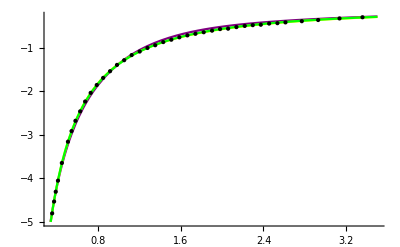

```mathematica
Plot[{Modelf[r],Modelf2[r],V[r]},{r,0.1,3.5},PlotStyle->{Purple,Yellow,Green},PlotRange->{{0,3.5},{0,-5}},AxesOrigin->{0,0},ImageSize->Full,Epilog->Point[TrueV]]
```

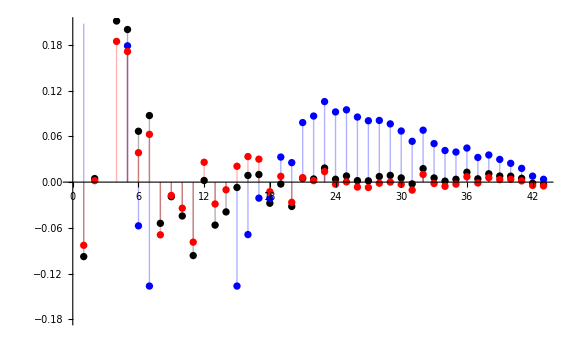

```mathematica
ListPlot[{Table[(Transpose[TrueV][[2]][[i]])^2-(V[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}],Table[(Transpose[TrueV][[2]][[i]])^2-(Modelf[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}],Table[(Transpose[TrueV][[2]][[i]])^2-(Modelf2[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}]},ImageSize->Large,Filling->Axis,PlotStyle->{Black,Blue,Red}]
```

```mathematica
α=2.;u0=1.*10^-8;
f[e_?NumberQ(*/;e∈Reals*)]:=
Block[{u,r,r1=1500.,r2=u0},
First[u[r2]/.
NDSolve[{u''[r]+(α(e-Modelf2[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==(*√(α(V[r1]-e)) u0*)-u0},
u,{r,r1,r2},Method->"Chasing",MaxSteps->Infinity,WorkingPrecision->20,MaxStepFraction->10^-3]]]
```

```mathematica
FindRoot[f[e]==0,{e,-0.0012,-0.0013},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (-0.0012+1/r+0.875409 Power[«2»] Power[«2»]+0.120009 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (-0.0013+1/r+0.875409 Power[«2»] Power[«2»]+0.120009 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (-0.00121527+1/r+0.875409 Power[«2»] Power[«2»]+0.120009 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→-0.0012943}

```mathematica
Lepageenergy={1.28711542,0.183325753,0.0703755485,0.0371495726,0.0229268241,0.0155492598,0.00534541931,0.00129205010}
```

{1.28712,0.183326,0.0703755,0.0371496,0.0229268,0.0155493,0.00534542,0.00129205}

```mathematica
i=8;
```

```mathematica
Abs[((e/.%255)+Lepageenergy[[i]])/Lepageenergy[[i]]]*100
```

0.174176

```mathematica
%235
```

{e→-0.00536445}